## 収束性のチェック

```mathematica
Clear["Global`*"]
(*NotebookEvaluate[FileNameJoin[{NotebookDirectory[],"../../../../mathematica_utilities/mathematica_plot_options.nb"}]]*)
NotebookEvaluate[FileNameJoin[{NotebookDirectory[],"mathematica_plot_options.nb"}]]
(*json="/Users/tomoaki/BEM/Tanizawa1996_H0d05_L1d8_quad_potential_water0d1/result.json"*)
(*json ="/Users/tomoaki/BEM/Tanizawa1996_H0d05_L1d8_quad_potential_water_no_float0d09/result.json"*)
(*json="/Users/tomoaki/BEM/Goring1979_DT0d05_ELEMpseudo_quad_ALEpseudo_quad_ALEPERIOD1_fast/result.json"*)

jsonLINEAR="/Volumes/home/BEM/Goring1979//Goring1979_DT0d05_MESHwater0d09.obj_ELEMlinear_ALElinear_ALEPERIOD1/result.json"
jsonQUAD="/Volumes/home/BEM/Goring1979//Goring1979_DT0d05_MESHwater0d09.obj_ELEMlinear_ALEpseudo_quad_ALEPERIOD1/result.json"
(*json="/Volumes/home/BEM/Goring1979/Goring1979Goring1979_DT0d05_ELEMlinear_ALEpseudo_quad_ALEPERIOD1_fast/result.json"*)
(*json="/Volumes/home/BEM/Goring1979/Goring1979_DT0d05_ELEMlinear_ALEpseudo_quad_ALEPERIOD1_middle/result.json"*)
jsonInfo[jsonQUAD]
```

{plot2Doption,plot3Doption,framelabel[xlabel_String,ylabel_String,size_:20],axeslabel2D[xlabel_String,ylabel_String,size_:20],axeslabel3D[xlabel_String,ylabel_String,zlabel_String,size_:20],axeslabel[labels_List,size_: 20],importData,jsonInfo,interpolateAndFourier[time_List,disp_List,timeSpan_List: {}],interpolateAndFourierTr[timedisp_List,timeSpan_List: {}],MyFourier[list_,n_],MyInverseFourier[list_,n_],MyDiscreteConvolve[f_,g_],MyDiscreteConvolveUsingCn[FourierGF_],Rv[q_],Rs[q_],W2dQdt[q_,w_],Q2Roll[{a_,b_,c_,d_}],Q2Pitch[{a_,b_,c_,d_}],Q2Yaw[{a_,b_,c_,d_}],getOmegaFromKandDepth[k_,h_],getOmegaFromLandDepth[L_,h_],getTFromLandDepth[L_,h_],getkFromTandDepth[T_,h_]}

/Volumes/home/BEM/Goring1979//Goring1979_DT0d05_MESHwater0d09.obj_ELEMlinear_ALElinear_ALEPERIOD1/result.json

/Volumes/home/BEM/Goring1979//Goring1979_DT0d05_MESHwater0d09.obj_ELEMlinear_ALEpseudo_quad_ALEPERIOD1/result.json

no. | title | length
1 | cpu_time | 73
2 | eq_of_motion | 73
3 | gauge1_intersection | 73
4 | gauge2_intersection | 73
5 | gauge3_intersection | 73
6 | gradPhi_worst_grad | 73
7 | gradPhi_worst_iteration | 73
8 | gradPhi_worst_value | 73
9 | simulation_time | 73
10 | wall_clock_time | 73
11 | water_E | 73
12 | water_EK | 73
13 | water_EP | 73
14 | water_face_size | 73
15 | water_point_size | 73
16 | water_volume | 73

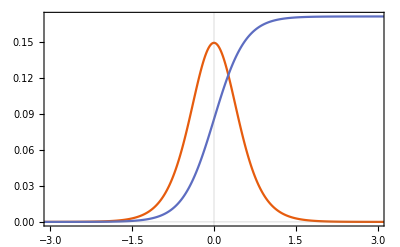

```mathematica
h=0.25;
H=0.1*h;
g=9.81;
c=Sqrt[g*(H+h)];
k=Sqrt[3*H/(4*h^3)];
eta[t_]:=H*Sech[k*(-c*(t))]^2

ListPlot[
{Table[{t,c*eta[t]/(h+eta[t])},{t,-5,5,0.01}],
Table[{t,NIntegrate[c*eta[T]/(h+eta[T]),{T,-Infinity,t}]},{t,-5,5,0.01}]},
PlotRange->{{-2/k*c,2/k*c},All},
Evaluate[plot2Doption]
]

(*ListPlot[
Table[{a,NIntegrate[c*eta[T]/(h+eta[T]),{T,-a/k*c,a/k*c}]},{a,0.5,5,0.1}],
PlotRange->All,
Evaluate[plot2Doption]
]*)
```

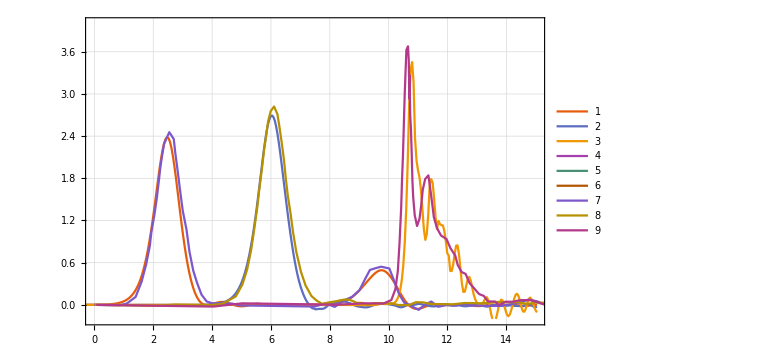

```mathematica
gauge1EXP=Import[FileNameJoin[{NotebookDirectory[],"Goring1979Gauge1.csv"}]];
gauge2EXP=Import[FileNameJoin[{NotebookDirectory[],"Goring1979Gauge2.csv"}]];
gauge3EXP=Import[FileNameJoin[{NotebookDirectory[],"Goring1979Gauge3.csv"}]];

h=0.25;
shiftt=4.96;
ListPlot[
{{importData[jsonLINEAR,"simulation_time"]-shiftt,(importData[jsonLINEAR,"gauge1_intersection",3]-h)*100}ᵀ,
{importData[jsonLINEAR,"simulation_time"]-shiftt,(importData[jsonLINEAR,"gauge2_intersection",3]-h)*100}ᵀ,
{importData[jsonLINEAR,"simulation_time"]-shiftt,(importData[jsonLINEAR,"gauge3_intersection",3]-h)*100}ᵀ,
{importData[jsonQUAD,"simulation_time"]-shiftt,(importData[jsonQUAD,"gauge1_intersection",3]-h)*100}ᵀ,
{importData[jsonQUAD,"simulation_time"]-shiftt,(importData[jsonQUAD,"gauge2_intersection",3]-h)*100}ᵀ,
{importData[jsonQUAD,"simulation_time"]-shiftt,(importData[jsonQUAD,"gauge3_intersection",3]-h)*100}ᵀ,
gauge1EXP,
gauge2EXP,
gauge3EXP}
,GridLines->Automatic
(*,Joined->{True,True,True,True,True,True,False,False,False}*)
,PlotLegends->Automatic
,ImageSize->Large
,PlotRange->{{0,15},{-0.2,4}}
,Evaluate[plot2Doption]]
```